2012311804 이병호 / 2016314728 정재헌

(#1) Table[] 함수를 사용하여 함수  f(x)=(sin(x))/x의 값을 n=1,2,...,10까지 x=nπ/10에서 구하여 list를 만들고 이를 이용하여 interpolating 함수를 작성하시오. 또 InterpolatingOrder의 값을 다르게 주어 비교하시오.

```mathematica
Clear["Global`*"]
```

{{π/10,(5 (-1+√5))/(2 π)},{π/5,(5 √(5/8-(√5)/8))/π},{(3 π)/10,(5 (1+√5))/(6 π)},{(2 π)/5,(5 √(5/8+(√5)/8))/(2 π)},{π/2,2/π},{(3 π)/5,(5 √(5/8+(√5)/8))/(3 π)},{(7 π)/10,(5 (1+√5))/(14 π)},{(4 π)/5,(5 √(5/8-(√5)/8))/(4 π)},{(9 π)/10,(5 (-1+√5))/(18 π)},{π,0}}

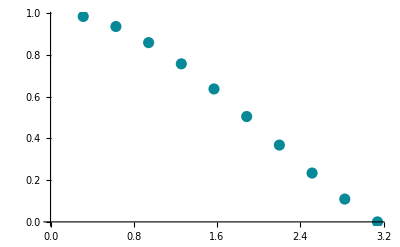

```mathematica
f[x_]:=Sin[x]/x
Data=Table[{(n*π)/10,f[(n*π)/10]},{n,1,10}]
inter0=ListPlot[Data, PlotStyle->PointSize[0.02]]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

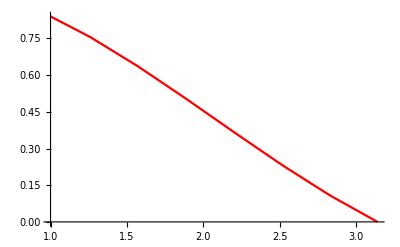

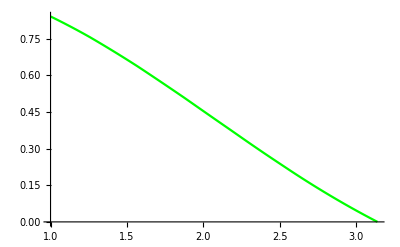

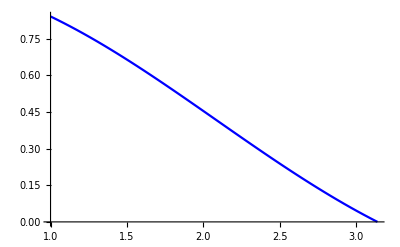

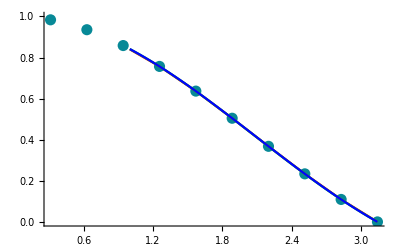

```mathematica
pump1=Interpolation[Data,InterpolationOrder->1]
pump2=Interpolation[Data,InterpolationOrder->2]
pump3=Interpolation[Data,InterpolationOrder->3]

inter1=Plot[Evaluate[pump1[n]],{n,1,π},PlotStyle->RGBColor[1,0,0]]
inter2=Plot[Evaluate[pump2[n]],{n,1,π},PlotStyle->RGBColor[0,1,0]]
inter3=Plot[Evaluate[pump3[n]],{n,1,π},PlotStyle->RGBColor[0,0,1]]

Show[inter0, inter1,inter2,inter3, PlotRange->{0,1}]
```

(#2) 다음의 표는 도시의 인구당 최저 기준의 fire flow rate를 보여준다. fire flow rate를 인구의 함수로 plot하고, 이의 interpolating polynomial 을 구하고, 인구가 115,000명일 때의 fire flow rate를 추정하시오.

                                                        [ Fire Flow Rates 기준표]                                         
                       population (1000) | Flow Rate (liter/second)
22 | 284
28 | 315
40 | 379
60 | 442
80 | 505
100 | 568
125 | 631
150 | 694
200 | 757

```mathematica
Clear["Global`*"]
```

InterpolatingFunction[…]

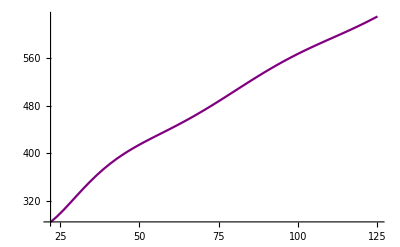

229875269108030427/284014902698267-(10632879765426029289 x)/124966557187237480+(68804353714678169147 x^2)/13632715329516816000-(196479169057149379048567 x^3)/1349638817622164784000000+(1697031590200775742341 x^4)/710336219801139360000000-(12548394245727404253997 x^5)/539855527048865913600000000+(178729217423977767101 x^6)/1349638817622164784000000000-(1783629359859361 x^7)/4380166548063820800000000+(5618650262090113 x^8)/10797110540977318272000000000

```mathematica
testdata={{22,284},{28,315},{40,379},{60,442},{80,505},{100,568},{125,631},{150,694},{200,757}};
pump4=Interpolation[testdata,InterpolationOrder->8]
inter4=Plot[Evaluate[pump4[n]],{n,22,125},PlotStyle->RGBColor[0.5,0,0.5]]
f[x_]=InterpolatingPolynomial[testdata,x]//Expand
```

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
f[115]//N
```

604.854

(#3)  다음의 data (frp) 를 잘 나타내는 함수들을 써서 표시하고 Plotting하시오.
               frp={{0,0},{0.4, 28.6},{1.2, 65.0},{4.0, 94.3}}
         (Hint: 본문 참조-Pop Quiz)

```mathematica
Clear["Global`*"]
```

{{0,0},{0.4,28.6},{1.2,65.},{4.,94.3}}

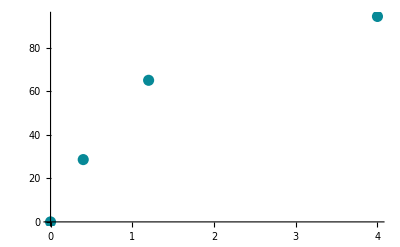

```mathematica
frp={{0,0},{0.4,28.6},{1.2,65.0},{4.0,94.3}}
point=ListPlot[frp,PlotStyle->PointSize[0.02]]
```

0.+81.5988 x-26.4405 x^2+2.98363 x^3

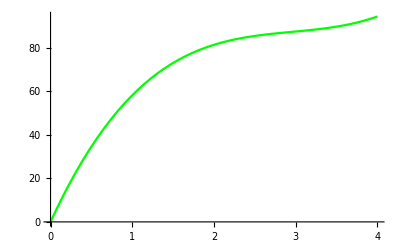

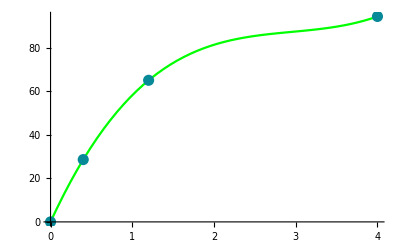

```mathematica
f=InterpolatingPolynomial[frp,x]//Expand
f1=Plot[f,{x,0,4},PlotStyle->RGBColor[0,1,0]]
Show[f1,point]
```

17.773+20.8586 x

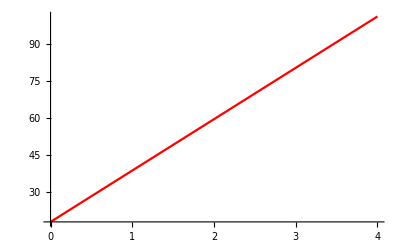

```mathematica
l1=Fit[frp,{1,x},x]
f2=Plot[l1,{x,0,4},PlotStyle->RGBColor[1,0,0]]
```

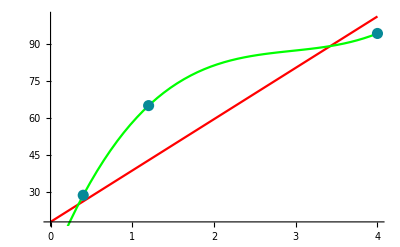

```mathematica
Show[f2,f1,point]
```

1.33525+66.9731 x-10.9369 x^2

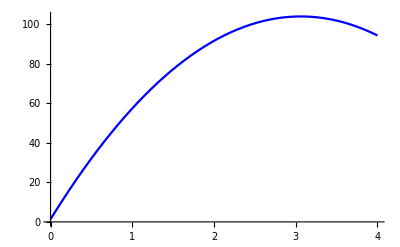

```mathematica
l2=Fit[frp,{1,x,x^2},x]
f3=Plot[l2,{x,0,4},PlotStyle->RGBColor[0,0,1]]
```

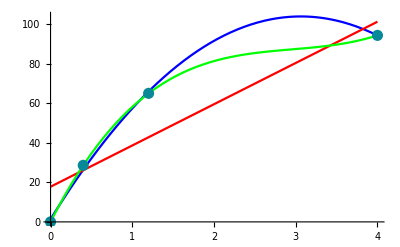

```mathematica
Show[f3,f2,f1,point]
```